## Load Package

```mathematica
Get[NotebookDirectory[]<>"RNAStructureIdentifier.wl"]
```

## Program Description

```mathematica
?Structure2Pair
```

Structure2Pair[s_]:=
Input: a structure s in dot-bracket notation.
Output: a pair table.

```mathematica
?MaxEntfBP
```

MaxEntfBP[esb_]:=
Input: an ensemble. 
Return:  the maximum entropy base pair.

```mathematica
?TreeMEBP
```

TreeMEBP[esb_,level_:10]: 
Input: an ensemble of secondary structures using pair tables. 
Return: a list {bp1,bp2,MEBPSpace,TreeSpace}, where
bp1--the set of all base pairs (i,j) for each structure in the ensemble,
bp2-- the vector of base pairs for each structure in the ensemble,
MEBPSpace-- the MEBPSpace of all maximum entropy base pairs of all clusters,
TreeSpace-- the TreeSpace containing all clusters, each level of clusters representing the ones containing the maximum entropy base pairs or not.

```mathematica
?RanPdtMEBP
```

RanPdtMEBP[TreeMEBP_,MFE_,esb_,lvl_:10,error_:0.01,error2_:0.05]: 
Input:
TreeMEBP, which is the output of TreeMEBP,
MFE, target structure,
esb, the ensemble of structures,
error: the error rate when the truthful answer is Yes,
error2: the error rate when the truthful answer is No.

Output: a list {str,ratio, leaveinfo, pathinfo}

str denotes the structure predicted in the leave.
ratio denotes the ratio of the predicted structure in the leave.

leaveinfo={leave,leavecorrectness}
leave: the leave ensemble at the end of the path.
leavecorrectness: whether choose a correct leaf.
1 represents correct, 0 represents wrong.

pathinfo={path, pathcorrectness,pathent,pathbpdist,bpset},

path: the path to the cluster closest to MFE.
      The path is a list of length 10.
      For i-th position, 
      1 represents that the predicted structure contains the i-th MEBP.
      2 represents that predicted does not contain the i-th MEBP.
      0 represnts that clustering stops.
pathcorrectness: the path correctness to the cluster closest to MFE.
        For i-th position, 1 represents correct, 0 represents wrong, -1 represents initial value.
pathent: the entropy of the cluster on the path. -1 represents initial value.
pathbpdist: bpdist between the cluster and MFE. -1 represents initial value.
bpset: the set of bias base pairs selected on the path.

```mathematica
?DrawESB
```

DrawESB[esb_]:=
Input: an ensemble of secondary structures using pair tables. 
Draw a secondary structure given by base pairs and theirs probabilities p.

```mathematica
?DrawTree
```

DrawTree[esb_,TreeMEBP_,lvl_]:=
Input an ensemble of secondary structures, and the output of TreeMEBP, and the max level of the tree (<=3).
Return the drawing of the tree of clusters, each level of clusters representing the ones containing the maximum entropy base pairs or not.

## Examples

### Import Data

Typically, an RNA secondary structure is represented in dot-bracket notation, such as “...((...((...)).....(((....)))...))......”.
Our programs utilize a pair table L to represent  a secondary structure. If base i is paired with base j, then position L_i stores j and position L_j stores i. If base k is unpaired, then position L_k stores 0. We provide a function to create a pair table from a dot-bracket notation as follows

```mathematica
Structure2Pair["...((...((...)).....(((....)))...))......"]
```

{0,0,0,35,34,0,0,0,15,14,0,0,0,10,9,0,0,0,0,0,30,29,28,0,0,0,0,23,22,21,0,0,0,5,4,0,0,0,0,0,0}

Given an RNA sequence, we obtain a Boltzmann ensemble of secondary structures via ViennaRNA. The output file contains structures in dot-bracket notation.
In the following we demonstrate how to create an input ensemble from such an output file.

```mathematica
rRNA5s=Import[NotebookDirectory[]<>"5srRNA/5s3_71.out"];
```

```mathematica
(*Create an ensemble of structures from output file.*)
rRNA5sESB=Map[Structure2Pair,Flatten[rRNA5s[[3;;1002]]]]
```

{{118,117,116,115,114,113,112,111,110,0,0,0,0,65,64,0,61,60,59,58,0,0,0,0,52,51,0,0,48,47,46,45,0,0,42,41,0,0,0,0,36,35,0,0,32,31,30,29,0,0,26,25,0,0,0,0,0,20,19,18,17,0,0,15,14,0,0,107,106,105,104,102,0,0,0,0,0,98,97,96,95,94,0,93,92,91,0,0,0,0,86,85,84,82,81,80,79,78,0,0,0,72,0,71,70,69,68,0,0,9,8,7,6,5,4,3,2,1},998,{0,0,116,115,114,113,112,111,110,0,0,0,0,65,64,62,61,60,59,58,0,0,0,0,52,68,82,81,80,79,78,0,0,0,76,0,75,74,73,72,0,0,9,8,7,6,5,4,3,0,0}}
 |  |  |  |

### Compute the ensemble tree

Once we have the ensemble,  we calculate the base pair having maximum entropy and its frequency.

```mathematica
MaxEntfBP[rRNA5sESB]
```

{{26,51},501}

The result shows that  the base pair having maximum entropy is (26,51) and its frequency is 501.

The ensemble tree  is  a hierarchical bi-partition of the ensemble of structures, utilizing base pairs having maximum entropy.
We can compute the ensemble tree in a single command.

```mathematica
rRNA5sTreeMEBP=TreeMEBP[rRNA5sESB];
```

### Visualizing the result

We present an ensemble of secondary structures as a greyscale diagram.

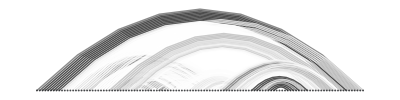

```mathematica
DrawESB[rRNA5sESB]
```

We visualize the ensemble tree, together with base pairs of maximum entropy. Here we set the maximum level to be 2.

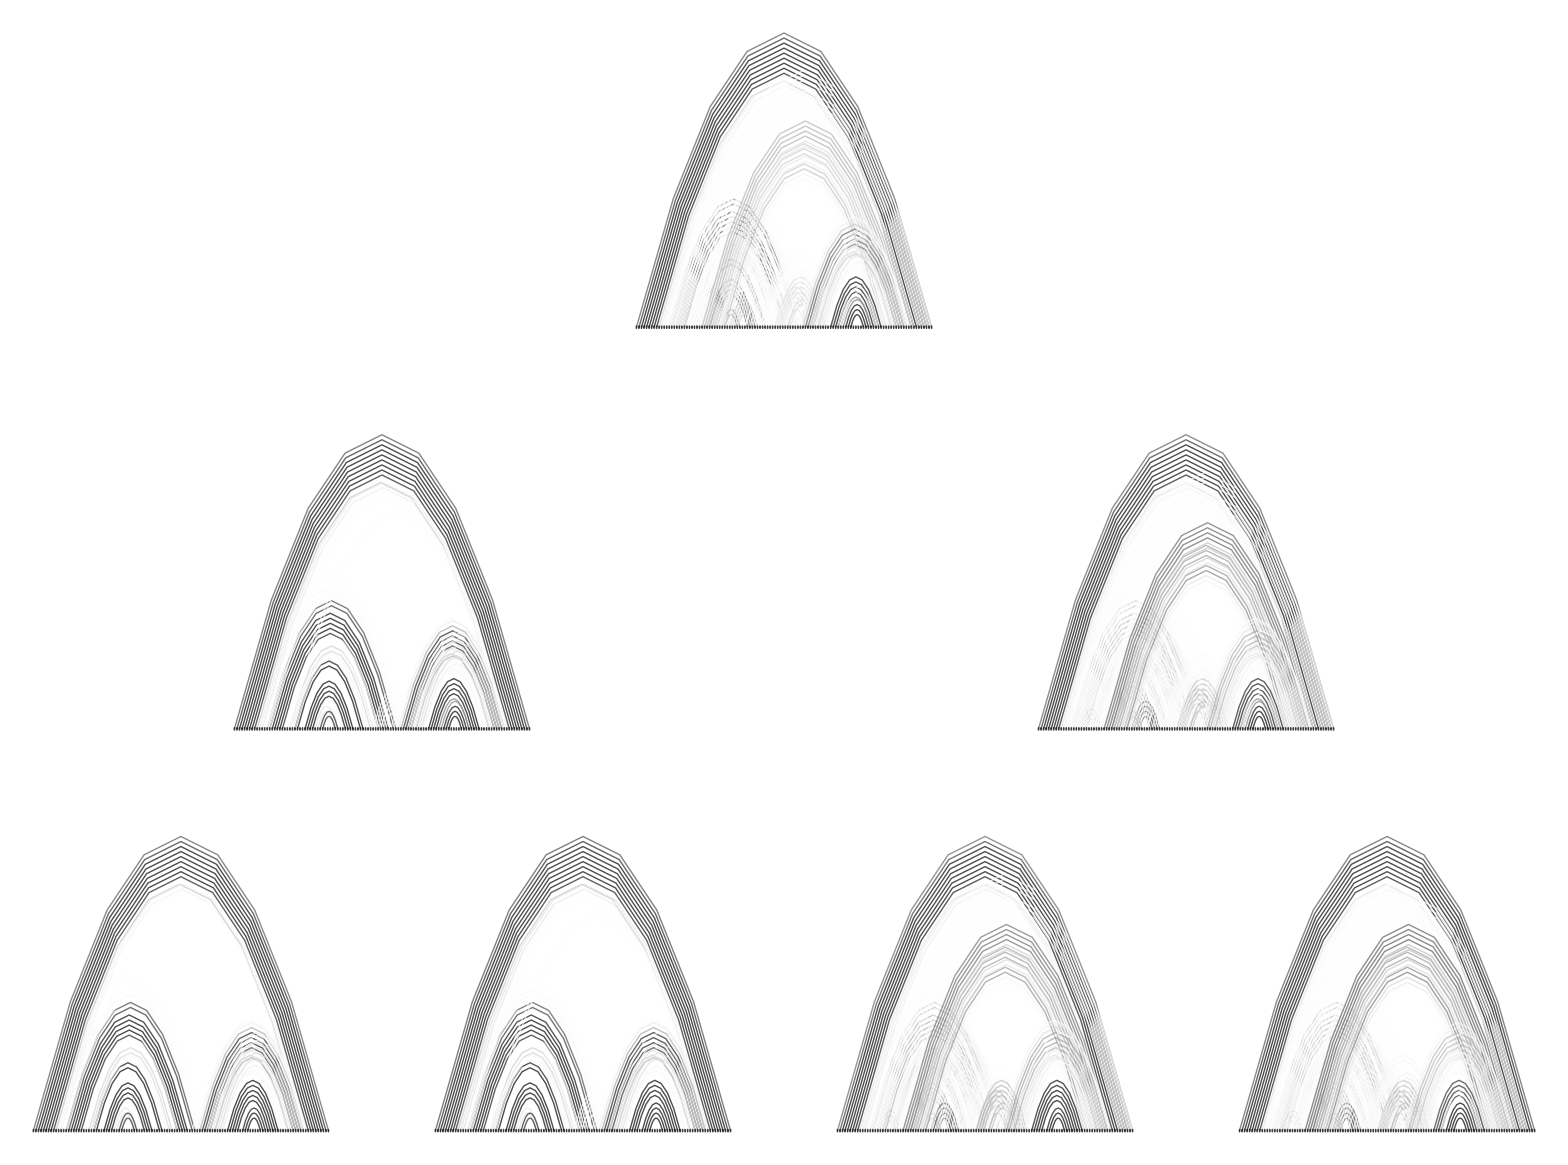

```mathematica
DrawTree[rRNA5sESB,rRNA5sTreeMEBP,2]
```